```mathematica
(*Check the simulation with realistic material and beam properties*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
```

```mathematica
(*Definitions*)
```

```mathematica
g = {0,9.81,0};
dat=Rationalize[{Ep*Iy->116.54916,Ep*Iz->116.54916,ρ*A->0.331}];
```

```mathematica
(*Functions*)
```

```mathematica
hom[rot_,trans_]:=Module[{},Return[Join[Join[rot,Transpose[{trans}],2],{{0,0,0,1}}]]];
```

```mathematica
(*Number of discretisations of the link, the number of links and length of each link*)
```

```mathematica
disc=3;
links = 1;
L = 5;
```

```mathematica
(*Shape functions of a simple rigid beam*)
```

```mathematica
ψ = Together[Expand[{1-3(s/lp)^2+2(s/lp)^3,s(s/lp-1)^2,(s/lp)^2(3-2 s/lp),s^2/lp(s/lp-1)}]]/.{lp->L/disc};
```

```mathematica
(*Number of rigid degrees of freedom*)
```

```mathematica
qr=Table[Symbol["θ"<>ToString[i]][t],{i,links}];
```

```mathematica
(*Number of flexible degrees of freedom per link. Each discretisation has 4 unique DoF. Includes the clamped DoF which needs to be enforced explicitly*)
```

```mathematica
qf=Table[Table[{Symbol["δy"<>ToString[i]<>ToString[j]][t], Symbol["ϕy"<>ToString[i]<>ToString[j]][t], Symbol["δz"<>ToString[i]<>ToString[j]][t], Symbol["ϕz"<>ToString[i]<>ToString[j]][t]},{j, disc+1}],{i, links}];
```

```mathematica
(*Computing the transformation matrices between the links*)
```

```mathematica
Tmatr = Table[Symbol["Tmatr"<>ToString[jj]],{jj, 1, links}];
```

```mathematica
Tmatr[[1]] =  hom[rotZ[qr[[1]]], {0,0,0}];
For[ii=2, ii≤links, ii++,
Tflex=hom[rotZ[qf[[ii-1, disc+1]][[4]]],{0,0,0}].hom[rotZ[0],{0,0,qf[[ii-1, disc+1]][[3]]}].hom[rotY[qf[[ii-1, disc+1]][[2]]],{0,0,0}].hom[rotY[0],{0,qf[[ii-1, disc+1]][[1]],0}];
Tmatr[[ii]] = Tmatr[[ii-1]].hom[rotZ[0], {L,0,0}].hom[rotZ[qr[[ii]]], {0,0,0}]*Tflex;
]
```

```mathematica
(*Generalised coordinates*)
```

```mathematica
q = Join[qr,Flatten[ qf[[;;, 2;;]]]];
```

```mathematica
boundary = Inner[Rule, Flatten[qf[[;;, 1]]], ConstantArray[0, Length[Flatten[qf[[;;, 1]]]]], List];
```

```mathematica
d2ψ = D[ψ, {s,2}];
```

```mathematica
(*Computation of the mass matrix*)
```

```mathematica
(*tempterm = ConstantArray[0,{Length[q], Length[q]}];
gterm = 0;
flexterm = 0;
For[jj=1, jj≤links, jj++,
For[ii=1, ii<disc+1, ii++,
(*For mass matrix*)
ptemp = Tmatr[[jj]][[1;;3, 4]]+(Tmatr[[jj]][[1;;3, 1;;3]]).{(ii-1)*L/disc+s, ψ.{qf[[jj,ii]][[1]], qf[[jj,ii]][[4]], qf[[jj,ii+1]][[1]], qf[[jj,ii+1]][[4]]}, ψ.{qf[[jj,ii]][[3]], qf[[jj,ii]][[2]], qf[[jj,ii+1]][[3]], qf[[jj,ii+1]][[2]]}};
tempterm =tempterm+(ρ*A* Integrate[Expand[Transpose[D[ptemp, {q}]].D[ptemp, {q}]], {s, 0, L/disc}])/.dat;
(*For gvector*)
gterm = gterm+(ρ*A*Integrate[g.ptemp,{s, 0, L/disc}])/.dat;
flexterm = flexterm+(Integrate[Together[Ep*Iy*(d2ψ.{qf[[jj,ii]][[1]], qf[[jj,ii]][[4]], qf[[jj,ii+1]][[1]], qf[[jj,ii+1]][[4]]})^2+Ep*Iz*(d2ψ.{qf[[jj,ii]][[3]], qf[[jj,ii]][[2]], qf[[jj,ii+1]][[3]], qf[[jj,ii+1]][[2]]})^2],{s, 0, L/disc}])/.dat;
Clear[ptemp];
]
]*)
```

```mathematica
tempterm = ConstantArray[0,{Length[q], Length[q]}];
gterm = 0;
flexterm = 0;
For[jj=1, jj≤links, jj++,
For[ii=1, ii<disc+1, ii++,
(*For mass matrix*)
ptemp = Tmatr[[jj]][[1;;3, 4]]+(Tmatr[[jj]][[1;;3, 1;;3]]).{(ii-1)*L/disc+s, ψ.{qf[[jj,ii]][[1]], qf[[jj,ii]][[4]], qf[[jj,ii+1]][[1]], qf[[jj,ii+1]][[4]]}, ψ.{qf[[jj,ii]][[3]], qf[[jj,ii]][[2]], qf[[jj,ii+1]][[3]], qf[[jj,ii+1]][[2]]}};
tempterm =tempterm+ρ*A*(Integrate[Expand[Transpose[D[ptemp, {q}]].D[ptemp, {q}]], {s, 0, L/disc}])/.dat;
(*For gvector*)
gterm = gterm+ρ*A*(Integrate[g.ptemp,{s, 0, L/disc}])/.dat;
flexterm = flexterm+(Integrate[Together[Ep*Iy/2*(d2ψ.{qf[[jj,ii]][[1]], qf[[jj,ii]][[4]], qf[[jj,ii+1]][[1]], qf[[jj,ii+1]][[4]]})^2+Ep*Iz/2*(d2ψ.{qf[[jj,ii]][[3]], qf[[jj,ii]][[2]], qf[[jj,ii+1]][[3]], qf[[jj,ii+1]][[2]]})^2],{s, 0, L/disc}])/.dat;
Clear[ptemp];
]
]
```

```mathematica
(*Impose conditions and reduce the size of the problem before writing the mass matrix*)
```

```mathematica
Mmat = tempterm/.boundary//Expand;
Mmat//Dimensions
```

{13,13}

```mathematica
(*Verifying property of mass matrix*)
```

```mathematica
Simplify[Transpose[Mmat]-Mmat]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Computing the centripetal and the Coriolis term*)
```

```mathematica
nn = Length[q];
tempC = Table[0, {ii, 1,nn}, {jj, 1,nn}];
For [ii= 1, ii≤ nn, 
For[jj = 1, jj ≤ nn,
For[kk = 1, kk≤ nn, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], q[[kk]]] + D[Mmat[[ii,kk]], q[[jj]]] - D[Mmat[[jj, kk]], q[[ii]]])*D[q[[kk]],t] ;
kk++];
jj++];
ii++];
```

```mathematica
(*Verifying property of Cmat*)
```

```mathematica
Amat = D[Mmat,t] - 2*tempC;
```

```mathematica
(Amat+ Transpose[Amat])//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Gravitational potential term assuming joint does not have any mass*)
```

```mathematica
Gvec = D[gterm/.boundary, {q}];
```

```mathematica
(*Elastic stiffness term. This is same as assembling stiffness matrix in FEM*)
```

```mathematica
Flex = D[flexterm/.dat/.boundary, {q}];
```

```mathematica
(*Total potential term*)
```

```mathematica
Gterm = Flex+Gvec;
```

```mathematica
(*Formulating the dynamics model*)
```

```mathematica
ruul = Inner[List,D[q,t], ConstantArray[_Real, {Length[q]}], List]
```

{{θ1'[t],_Real},{δy12'[t],_Real},{ϕy12'[t],_Real},{δz12'[t],_Real},{ϕz12'[t],_Real},{δy13'[t],_Real},{ϕy13'[t],_Real},{δz13'[t],_Real},{ϕz13'[t],_Real},{δy14'[t],_Real},{ϕy14'[t],_Real},{δz14'[t],_Real},{ϕz14'[t],_Real}}

```mathematica
cMmat = Compile[{{θ1[t],_Real},{δy12[t],_Real},{ϕy12[t],_Real},{δz12[t],_Real},{ϕz12[t],_Real},{δy13[t],_Real},{ϕy13[t],_Real},{δz13[t],_Real},{ϕz13[t],_Real},{δy14[t],_Real},{ϕy14[t],_Real},{δz14[t],_Real},{ϕz14[t],_Real}}, Evaluate[Mmat]];
```

```mathematica
cMmat@@RandomReal[{0,100},Length[Mmat]]//MatrixForm;
```

```mathematica
cCmat = Compile[{{θ1[t],_Real},{δy12[t],_Real},{ϕy12[t],_Real},{δz12[t],_Real},{ϕz12[t],_Real},{δy13[t],_Real},{ϕy13[t],_Real},{δz13[t],_Real},{ϕz13[t],_Real},{δy14[t],_Real},{ϕy14[t],_Real},{δz14[t],_Real},{ϕz14[t],_Real}, {θ1'[t],_Real},{δy12'[t],_Real},{ϕy12'[t],_Real},{δz12'[t],_Real},{ϕz12'[t],_Real},{δy13'[t],_Real},{ϕy13'[t],_Real},{δz13'[t],_Real},{ϕz13'[t],_Real},{δy14'[t],_Real},{ϕy14'[t],_Real},{δz14'[t],_Real},{ϕz14'[t],_Real}}, Evaluate[tempC]];
```

```mathematica
cCmat@@RandomReal[{0,100},Length[q]*2];
```

```mathematica
cGvec = Compile[{{θ1[t],_Real},{δy12[t],_Real},{ϕy12[t],_Real},{δz12[t],_Real},{ϕz12[t],_Real},{δy13[t],_Real},{ϕy13[t],_Real},{δz13[t],_Real},{ϕz13[t],_Real},{δy14[t],_Real},{ϕy14[t],_Real},{δz14[t],_Real},{ϕz14[t],_Real}}, Evaluate[Gterm]];
```

```mathematica
cGvec@@RandomReal[{0,100},Length[q]]
```

{612.839,5686.92,6156.11,7746.04,-8544.4,24092.,24346.9,30586.4,10311.2,-21161.9,34328.4,-34722.8,22235.4}

```mathematica
(*Equations of motion*)
```

```mathematica
(*Formulating the double dots*)
τ = Join[{0}, ConstantArray[0, Length[q]-1]];
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval, LHS},
Mval=cMmat@@q;
Cval=cCmat@@Join[q,dq];
Gval=cGvec@@q;
LHS=-(Inverse[Mval]).(Cval.dq+Gval-τ);
Return[LHS];
];
```

```mathematica
doubledots[RandomReal[{0,10},Length[q]],RandomReal[{0,10},Length[q]]]
```

{-273.432,-64562.7,29315.7,3895.22,-469385.,-39187.2,8497.78,-9280.14,-921382.,-310089.,-111756.,-22411.,-2.00726×10^6}

```mathematica
tf = 10;
dynsim = NDSolve[{doubledots[q1[t],q1'[t]]==q1''[t],q1[0]==Join[{π/6},Table[0,{jj,Length[q]-1}]],q1'[0]==Table[0,{jj,Length[q]}]},q1,{t,0,tf}, AccuracyGoal->15][[1]]
```

{q1→InterpolatingFunction[{{0., 10.}}, <>]}

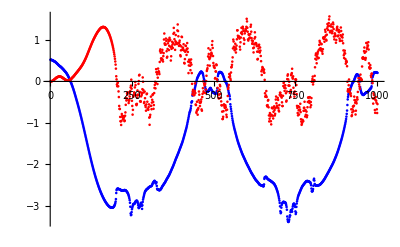

```mathematica
θ1list = Table[((q1/.dynsim)[tt])[[1]],{tt, 0, tf, 0.01}];
θ2list = Table[((q1/.dynsim)[tt])[[13]],{tt, 0, tf, 0.01}];
Show[ListPlot[θ1list, PlotStyle->Blue], ListPlot[θ2list, PlotStyle->Red], PlotRange->All]
```

```mathematica
(*Visualisation*)
```

```mathematica
(*Taking data from solution*)
```

```mathematica
coords = Table[((q1/.dynsim)[tt]),{tt, 0, tf, 0.01}];
```

```mathematica
δy12list = Table[((q1/.dynsim)[tt])[[2]],{tt, 0, tf, 0.01}];
ϕy12list = Table[((q1/.dynsim)[tt])[[3]],{tt, 0, tf, 0.01}];
δz12list = Table[((q1/.dynsim)[tt])[[4]],{tt, 0, tf, 0.01}];
ϕz12list = Table[((q1/.dynsim)[tt])[[5]],{tt, 0, tf, 0.01}];
δy13list = Table[((q1/.dynsim)[tt])[[6]],{tt, 0, tf, 0.01}];
ϕy13list = Table[((q1/.dynsim)[tt])[[7]],{tt, 0, tf, 0.01}];
δz13list = Table[((q1/.dynsim)[tt])[[8]],{tt, 0, tf, 0.01}];
ϕz13list = Table[((q1/.dynsim)[tt])[[9]],{tt, 0, tf, 0.01}];
δy14list = Table[((q1/.dynsim)[tt])[[10]],{tt, 0, tf, 0.01}];
ϕy14list = Table[((q1/.dynsim)[tt])[[11]],{tt, 0, tf, 0.01}];
δz14list = Table[((q1/.dynsim)[tt])[[12]],{tt, 0, tf, 0.01}];
ϕz14list = Table[((q1/.dynsim)[tt])[[13]],{tt, 0, tf, 0.01}];
```

```mathematica
(*The end tip position*)
```

```mathematica
ii = disc;
jj = 1;
tip = Tmatr[[1]][[1;;3, 4]]+(Tmatr[[1]][[1;;3, 1;;3]]).{(ii-1)*L/disc+s, ψ.{qf[[jj,ii]][[1]], qf[[jj,ii]][[4]], qf[[jj,ii+1]][[1]], qf[[jj,ii+1]][[4]]}, ψ.{qf[[jj,ii]][[3]], qf[[jj,ii]][[2]], qf[[jj,ii+1]][[3]], qf[[jj,ii+1]][[2]]}}/.s->L/disc;
```

```mathematica
anypoint = ConstantArray[0, {disc, 3}];
For[ii=1, ii<disc+1, ii++,
anypoint[[ii]] = Tmatr[[1]][[1;;3, 4]]+(Tmatr[[1]][[1;;3, 1;;3]]).{(ii-1)*L/disc+s, ψ.{qf[[jj,ii]][[1]], qf[[jj,ii]][[4]], qf[[jj,ii+1]][[1]], qf[[jj,ii+1]][[4]]}, ψ.{qf[[jj,ii]][[3]], qf[[jj,ii]][[2]], qf[[jj,ii+1]][[3]], qf[[jj,ii+1]][[2]]}};
]
```

```mathematica
(*Now we shall sample three points in between along with the nodes*)
```

```mathematica
sample = {0, 1/4*L/disc, 1/2*L/disc, 3/4*L/disc, L/disc};
```

```mathematica
allpts = Table[Table[anypoint[[dd]]/.s->sample[[d]]/.boundary,{d, 1, Length[sample]}],{dd, 1, disc}];
```

```mathematica
flexsim = Manipulate[Show[Graphics3D[{Thickness[0.01], Line[Flatten[allpts, 1]]}, PlotRange->{{-7, 7}, {-7,7},{-2, 2}}, AspectRatio->1, ViewPoint->Top], Graphics3D[{Red, Sphere[{0,0,0}, 0.3]}]]/.Inner[Rule, q, coords[[uu]], List],{uu, 1, Length[coords], 1, AnimationRate->150}]
```

```mathematica
(*A smooth way to save the work done in gif format*)
```

```mathematica
Export["flexsim.gif",flexsim, "AnimationDuration"-> 10]
```

flexsim.gif

```mathematica
tiplist = Table[tip/.{θ1[t]->θ1list[[kk]], δy14[t]->δy14list[[kk]], δz14[t]->δz14list[[kk]]}, {kk, 1, Length[θ1list]}];
```

```mathematica
(*Motion of the end-tip*)
```

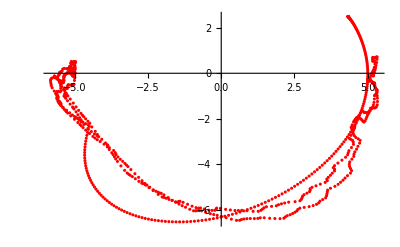

```mathematica
ListPlot[tiplist[[;;, 1;;2]], PlotStyle->Red]
```

```mathematica
(*Taking out the flexible part of the mass and stiffness matrix*)
```

```mathematica
Mff = Mmat[[2;;, 2;;]];
```

```mathematica
Kff = Table[Table[Coefficient[Flex[[jj]], q[[ii]]],{ii, 2, Length[q]}],{jj, 2, Length[Flex]}];
```

```mathematica
N[Sqrt[Eigenvalues[Inverse[Mff].Kff/.θ1[t]->0]]]
```

{396.157,396.157,198.713,198.713,105.586,105.586,46.8861,46.8861,16.5931,16.5931,2.63934,2.63934}

```mathematica
(*When the number of links is increased to 2 the dynamics betwen them changes. Needs fix.*)
```

```mathematica
(*Next step is to see how position control works and then implement input-shaping control. That ends one thought.*)
```